```mathematica
data=Table[
With[{g=Graph[plantri[[k]]]},
{ChromaticPolynomial[g,x],ChromaticPolynomial[DualGraph[Faces[g]],x]}
]
,{k,7,7}]
```

{{72007008 x-355009664 x^2+808062888 x^3-1137507794 x^4+1116439755 x^5-814730131 x^6+459259781 x^7-204591612 x^8+72921212 x^9-20879569 x^10+4786675 x^11-868893 x^12+122328 x^13-12900 x^14+960 x^15-45 x^16+x^17,-1928260072 x+17219828884 x^2-76660399298 x^3+227618006203 x^4-507903714367 x^5+908453964885 x^6-1354763457383 x^7+1728104769710 x^8-1918178007854 x^9+1874667316366 x^10-1626207568987 x^11+1258951855377 x^12-872868233611 x^13+543081124665 x^14-303447878108 x^15+152213158429 x^16-68447386268 x^17+27524654992 x^18-9862131655 x^19+3132983526 x^20-876715748 x^21+214288617 x^22-45247800 x^23+8135020 x^24-1221262 x^25+148983 x^26-14190 x^27+990 x^28-45 x^29+x^30}}

```mathematica
TableForm[Table[TableForm[Map[CompleteBaseCoeff[#]&,data[[k]]]],{k,1,1}]]
```

0 | 0 | 0 | 0 | 16 | 34896 | 1779860 | 17151824 | 55294938 | 78223766 | 56476391 | 22766703 | 5401605 | 773706 | 66900 | 3380 | 91 | 1 |  |  |  |  |  |  |  |  |  |  |  |  | 
0 | 0 | 0 | 227584 | 100855826860 | 324010835509000 | 82165327834538842 | 4224537877362017025 | 70810049721539414108 | 508420370444290272408 | 1856467659568269553576 | 3867725935146430427854 | 4985307302783562265282 | 4217510946659294546795 | 2447812408863221316983 | 1008168932646545193182 | 302437169785812105713 | 67423638479691816460 | 11342797628154595800 | 1456377941741327005 | 143828993447961346 | 10973756967833994 | 647508442927812 | 29467587908770 | 1026947522920 | 27053688113 | 527378244 | 7348305 | 68995 | 390 | 1

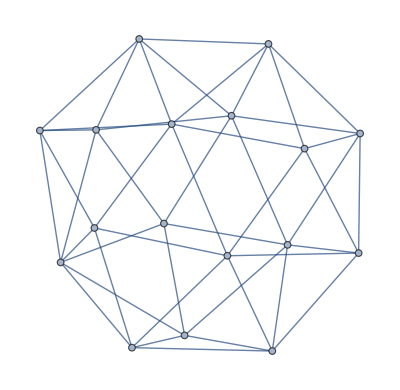

```mathematica
g89=Graph[plantri[[7]]]
```

```mathematica
ChromaticPolynomial[g89,x]
```

72007008 x-355009664 x^2+808062888 x^3-1137507794 x^4+1116439755 x^5-814730131 x^6+459259781 x^7-204591612 x^8+72921212 x^9-20879569 x^10+4786675 x^11-868893 x^12+122328 x^13-12900 x^14+960 x^15-45 x^16+x^17

```mathematica
FlowPolynomial[g89,x]
```

-1928260072+17219828884 x-76660399298 x^2+227618006203 x^3-507903714367 x^4+908453964885 x^5-1354763457383 x^6+1728104769710 x^7-1918178007854 x^8+1874667316366 x^9-1626207568987 x^10+1258951855377 x^11-872868233611 x^12+543081124665 x^13-303447878108 x^14+152213158429 x^15-68447386268 x^16+27524654992 x^17-9862131655 x^18+3132983526 x^19-876715748 x^20+214288617 x^21-45247800 x^22+8135020 x^23-1221262 x^24+148983 x^25-14190 x^26+990 x^27-45 x^28+x^29

```mathematica
FlowPolynomial[DualGraph[Faces[g89]],x]*x==ChromaticPolynomial[g89,x]//Simplify
```

True

```mathematica
ChromaticPolynomial[CompleteGraph[3],x]
```

2 x-3 x^2+x^3

```mathematica
Plot3D[TuttePolynomial[DualGraph[Faces[CompleteGraph[2]]],{x,y}],{x,-10,10},{y,-10,10}]
```

-Graphics3D-

```mathematica
TuttePolynomial[CompleteGraph[4],{x,y}]
```

2 x+3 x^2+x^3+2 y+4 x y+3 y^2+y^3

```mathematica
Table[With[{g=allGraphs[k,"graph"]},g->Graph[DualGraph[Faces[g]],GraphLayout->"TutteEmbedding",VertexStyle->Red,ImageSize->{50,50},EdgeStyle->Darker[Darker[Green]]]],{k,atomKeys}]//TableForm
```

-Graphics-→
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-

```mathematica
Select[Keys[allGraphs],With[{g=allGraphs[#,"graph"]},VertexCount[g]==5 && EdgeCount[g]==5 &&
EdgeQ[g,1<->3]&&
EdgeQ[g,2<->4]&&
EdgeQ[g,3<->5]&&
EdgeQ[g,4<->1]&&
EdgeQ[g,5<->2]
]&]
```

{8859}

```mathematica
Labeled[allGraphs[8859,"graph"],Style[allGraphs[8859,"colofour"],ColourForKey[allGraphs,8859]]]
```

-Graphics-v12x34x5+v12x3x45+v12x3x4x5+v15x23x4+v15x2x34+v15x2x3x4+v1x23x45+v1x23x4x5+v1x2x34x5+v1x2x3x45+v1x2x3x4x5

```mathematica
allGraphs[8859,"colofour"]/.repcolofourgraph2
```

-Graphics-v12x34x549216+-Graphics-v12x3x4549208+-Graphics-v15x23x430496+-Graphics-v1x23x4529768+-Graphics-v15x2x3430262+-Graphics-v12x3x4x549207+-Graphics-v1x23x4x529767+-Graphics-v1x2x34x529533+-Graphics-v15x2x3x430253+-Graphics-v1x2x3x4529525+-Graphics-v1x2x3x4x529524

```mathematica
allGraphs[lambdaKey,"colofour"]/.repcolofourgraph2
```

-Graphics-v13x24x536166+-Graphics-v13x25x436112+-Graphics-v14x25x331738+-Graphics-v14x2x3531714+-Graphics-v1x24x3529608+-Graphics-v13x2x4x536085+-Graphics-v14x2x3x531711+-Graphics-v1x24x3x529605+-Graphics-v1x25x3x429551+-Graphics-v1x2x35x429527+-Graphics-v1x2x3x4x529524

```mathematica
allGraphs[quad1Key,"colofour"]/.repcolofourgraph2
```

-Graphics-v13x2x4x536085

```mathematica
ChromaticPolynomial[allGraphs[8859,"graph"],x]
```

4 x-10 x^2+10 x^3-5 x^4+x^5

```mathematica
ChromaticPolynomial[allGraphs[lambdaKey,"graph"],x]
```

4 x-10 x^2+10 x^3-5 x^4+x^5

```mathematica
FlowPolynomial[allGraphs[8859,"graph"],x]
```

-1+x

```mathematica
FlowPolynomial[allGraphs[lambdaKey,"graph"],x]
```

-1+x

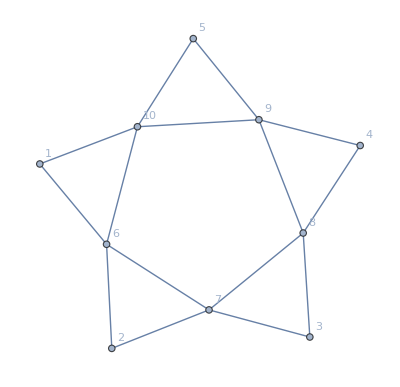

```mathematica
Graph[EdgeDelete[gr7[10],{1<->2,2<->3,3<->4,4<->5,5<->1}],GraphLayout->"SpringElectricalEmbedding"]
```